## Basic Formulas

```mathematica
mpi=0.13957018;
mk=0.493677;
mp=0.938272013;
T0={0.08,0.1,0.12};
q0={1.05,1.1,1.15};
Clear[q];Clear[T];
fMT[q_,T_,m_,μ_,p_]:=(1+((q-1)(√(p^2+m^2)-μ))/T)^(-1/(q-1)); 
(*MT for Maxwell-Boltzmann particle distribution function in Tsallis-2 Statistics*)
fFT[q_,T_,m_,μ_,p_]:=1/((1+((q-1)(√(p^2+m^2)-μ))/T)^(q/(q-1))+1); 
(*FT for Fermi-Dirac particle distribution in Tsallis-2 Stastitics*)
fBT[q_,T_,m_,μ_,p_]:=1/((1+((q-1)(√(p^2+m^2)-μ))/T)^(q/(q-1))-1); 
(*BT for Bose-Einstein particle distribution in Tsallis-2 Stastitics*)
fMB[T_,m_,μ_,p_]:=E^((-Sqrt[m^2+p^2]+μ)/T);(*MB Stands for Maxwell-Boltzmann distribution function in Boltzmann-Gibbs Statistics*)
fFB[T_,m_,μ_,p_]:=E^(μ/T)/(E^(Sqrt[m^2+p^2]/T)+E^(μ/T));
(*FB Stands for Fermi-Dirac distribution function in Boltzmann-Gibbs Statistics*)
fBB[T_,m_,μ_,p_]:=E^(μ/T)/(E^(Sqrt[m^2+p^2]/T)-E^(μ/T));
(*BB Stands for Bose-Einstein distribution function in Boltzmann-Gibbs Statistics*)
PInt[q_,T_,m_,g_,func_Symbol]:=g/(6 π^2)p^4/(√(p^2+m^2))(func[q,T,m,0,p])^q;
(*The pressure integrand form which will case by case*)
```

## π^+ (Classical) single particle distribution in Tsallis & Boltzmann Statistics (T&B Stat) - Var (q)

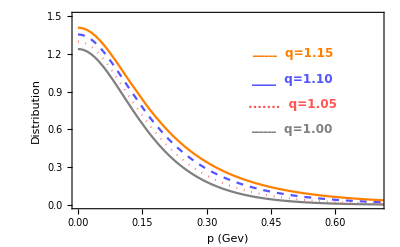

```mathematica
f1=fMB[#1,#2,0,p]&[T0[[2]],mpi];
f2=fMT[#1,#2,mpi,0,p]&[q0,T0[[2]]];
ScaledDistributions=5*Reverse[Append[Reverse[f2],f1]];
Plot[ScaledDistributions,{p,0,2},PlotRange->{{0,0.7},{0,1.5}},PlotStyle->{{Gray},{Dotted,Lighter[Red]},{Dashed,Lighter[Blue]},Orange},Frame->True,FrameLabel->{{"Distribution",None},{"p (Gev)",None}},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.004],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],Epilog->Reverse[{Inset[Style["ــــــ  q=1.00",12,Bold,FontFamily->"Times New Roman",FontColor->Gray,FontSlant->Italic],{0.5,0.6}],Inset[Style[".......  q=1.05",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Red],FontSlant->Italic],{0.5,0.8}],Inset[Style["____  q=1.10",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Blue],FontSlant->Italic],{0.5,1}],Inset[Style["ــــــ  q=1.15",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Orange,FontSlant->Italic],{0.5,1.2}]}]]
```

## π^+ (Boson) single particle distribution in Tsallis & Boltzmann Statistics (T&B Stat) - Var (q)

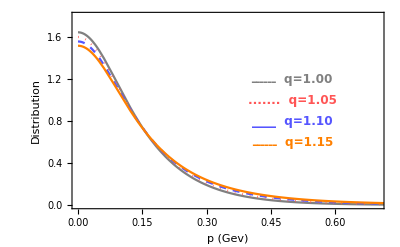

```mathematica
f1=fBB[#1,#2,0,p]&[T0[[2]],mpi];
f2=fBT[#1,#2,mpi,0,p]&[q0,T0[[2]]];
ScaledDistributions=5*Reverse[Append[Reverse[f2],f1]];
Plot[ScaledDistributions,{p,0,2},PlotRange->{{0,0.7},{0,1.8}},PlotStyle->{{Gray},{Dotted,Lighter[Red]},{Dashed,Lighter[Blue]},Orange},Frame->True,FrameLabel->{{"Distribution",None},{"p (Gev)",None}},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.004],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],Epilog->{Inset[Style["ــــــ  q=1.00",12,Bold,FontFamily->"Times New Roman",FontColor->Gray,FontSlant->Italic],{0.5,1.2}],Inset[Style[".......  q=1.05",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Red],FontSlant->Italic],{0.5,1}],Inset[Style["____  q=1.10",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Blue],FontSlant->Italic],{0.5,0.8}],Inset[Style["ــــــ  q=1.15",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Orange,FontSlant->Italic],{0.5,0.6}]}]
```

## π^+ (Boson) single particle distribution in Tsallis Statistics - Var (T)

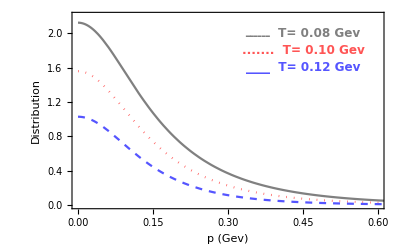

```mathematica
f2=fBT[#1,#2,mpi,0,p]&[q0[[2]],T0];
ScaledDistribution=5*Reverse[f2];
Plot[ScaledDistribution,{p,0,2},PlotRange->{{0,0.6},{0,2.2}},PlotStyle->{{Gray},{Dotted,Lighter[Red]},{Dashed,Lighter[Blue]},Orange},Frame->True,FrameLabel->{{"Distribution",None},{"p (Gev)",None}},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.004],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],Epilog->{Inset[Style["ــــــ  T= 0.08 Gev",12,Bold,FontFamily->"Times New Roman",FontColor->Gray,FontSlant->Italic],{0.45,2}],Inset[Style[".......  T= 0.10 Gev",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Red],FontSlant->Italic],{0.45,1.8}],Inset[Style["____  T= 0.12 Gev",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Blue],FontSlant->Italic],{0.45,1.6}]}]
```

## 2D Pressure Plot as function of Temperature for π^+ & K^+ (T&B Stat) [q=1.1]

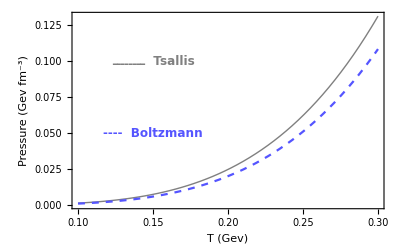

```mathematica
(*The mass difference between both particles is not so significant in the final result*)
(*Clear[PBB,PBT]*)
PBB[Tb_,pb_]:=(5.068)^3/(6 π^2)pb^4/(√(pb^2+mpi^2))fBB[Tb,mpi,0,pb];
PBT[Tt_,pt_]:=(5.068)^3/(6 π^2)pt^4/(√(pt^2+mpi^2))(fBT[1.1,Tt,mpi,0,pt])^1.1;
Plot[{NIntegrate[PBT[T1,p1],{p1,0,Infinity}],NIntegrate[PBB[T1,p1],{p1,0,Infinity}]},{T1,0.1,0.3},PlotStyle->{{Thick,Gray},{Dashed,Lighter[Blue]}},Frame->True,FrameLabel->{{"Pressure (Gev fm^-3)",None},{"T (Gev)",None}},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.004],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],Epilog->{Inset[Style["ــــــــ  Tsallis",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Gray,FontSlant->Italic],{0.15,0.1}],Inset[Style["----  Boltzmann",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Blue],FontSlant->Italic],{0.15,0.05}]}]
```

## 2D Pressure Plot for p as function of temperature (T&B Stat) [q=1.1]

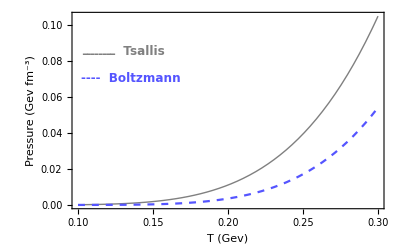

```mathematica
(*Clear[PFB,PBT]*)
PFB[Tb_,pb_]:=(2(5.068)^3)/(6 π^2)pb^4/(√(pb^2+mp^2))fFB[Tb,mp,0,pb];
PFT[Tt_,pt_]:=(2(5.068)^3)/(6 π^2)pt^4/(√(pt^2+mp^2))(fFT[1.1,Tt,mp,0,pt])^1.1;
Plot[{NIntegrate[PFT[T1,p1],{p1,0,Infinity}],NIntegrate[PFB[T1,p1],{p1,0,Infinity}]},{T1,0.1,0.3},PlotStyle->{{Thick,Gray},{Dashed,Lighter[Blue]}},Frame->True,FrameLabel->{{"Pressure (Gev fm^-3)",None},{"T (Gev)",None}},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.005],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],Epilog->{Inset[Style["ــــــــ  Tsallis",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Gray,FontSlant->Italic],{0.13,0.085}],Inset[Style["----  Boltzmann",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Blue],FontSlant->Italic],{0.135,0.07}]}]
```

## 2D Pressure Plot for p as function of q (T&B Stat) [T=0.1 Gev]

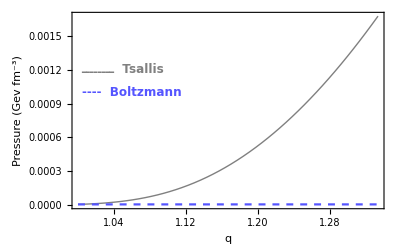

```mathematica
(*Clear[PFB,PBT]*)
PFBB[pb_]:=(2(5.068)^3)/(6 π^2)pb^4/(√(pb^2+mp^2))fFB[0.1,mp,0,pb];
PFBT[qt_,pt_]:=(2(5.068)^3)/(6 π^2)pt^4/(√(pt^2+mp^2))(fFT[qt,0.1,mp,0,pt])^qt;
Plot[{NIntegrate[PFBT[q1,p1],{p1,0,Infinity}],NIntegrate[PFBB[p1],{p1,0,Infinity}]},{q1,1,4/3},PlotStyle->{{Thick,Gray},{Dashed,Lighter[Blue]}},Frame->True,FrameLabel->{{"Pressure (Gev fm^-3)",None},{"q",None}},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.005],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],Epilog->{Inset[Style["ــــــــ  Tsallis",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Gray,FontSlant->Italic],{1.05,0.0006*2}],Inset[Style["----  Boltzmann",12,Red,Bold,FontFamily->"Times New Roman",FontColor->Lighter[Blue],FontSlant->Italic],{1.06,0.0005*2}]}]
```

## 3D Pressure Plot for π^+; Bose-Einstein Distribution (Tsallis Statistics)

```mathematica
Plot3D[NIntegrate[(2(5.068)^3)/(6 π^2)p^4/(√(p^2+mp^2))(fFT[q,T,mp,0,p])^q,{p,0,Infinity}],{q,1,1.3},{T,0.1,0.5},AxesLabel->{"q","T (GeV)","P (Gev.fm^-3)"},PlotStyle->Directive[Lighter[Red],Thickness[0.004],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain],BoundaryStyle->Thick]
```

-Graphics3D-

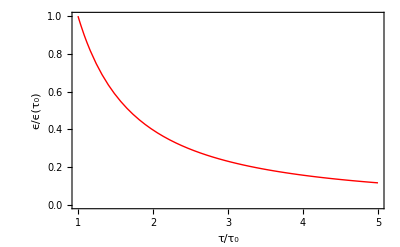

```mathematica
Plot[1/t^(4/3),{t,1,5},PlotStyle->{Thick,Red},Frame->True,FrameLabel->{{"ϵ/ϵ(τ_0)",None},{"τ/τ_0",None}},AxesOrigin->{1,0},FrameStyle->Directive[Darker[Darker[Black]],Thickness[0.005],14,Bold,FontFamily->"Times New Roman",FontSlant->Plain]]
```